```mathematica
Quit[]
```

```mathematica
$LoadAddOns={"FeynArts","FeynHelpers"};
Needs["FeynCalc`"]
```

FeynCalc 9.3.1 (stable version). For help, use the documentation center, check out the wiki or visit the forum.

To save your and our time, please check our FAQ for answers to some common FeynCalc questions.

See also the supplied examples. If you use FeynCalc in your research, please cite

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 256 (2020) 107478, arXiv:2001.04407.

• V. Shtabovenko, R. Mertig and F. Orellana, Comput.Phys.Commun. 207 (2016) 432-444, arXiv:1601.01167.

• R. Mertig, M. Böhm, and A. Denner, Comput. Phys. Commun. 64 (1991) 345-359.

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
CKM = IndexDelta;
Neglect[ME] = Neglect[ME2] = 0;
$FAVerbose=1;
(* use generic model from FeynCalc! The SUNF and SUNT functions in the .mod file have to be replaced by FASUNF and FASUNT *)
SetOptions[InsertFields, Model ->"../../FA_models/SMS-stop-FA/SMS-stop-FA",ExcludeParticles->{S[1]},InsertionLevel-> {Particles}];
SetOptions[Paint, PaintLevel -> {Particles}];
SetOptions[CreateTopologies, ExcludeTopologies -> {TadpoleCTs,Tadpoles, WFCorrectionCTs,SelfEnergyCTs}];
```

## g- t- t (1-loop)

The choice below for the momenta and the ordering of the particles in the process is equivalent to the correct
ordering for computing the effective vertex for the UFO format:
0 →3, with {} →{-F[9],F[9],V[4]} and all the momenta set as outgoing ({} → {p1,p2,p3}).
However the choice below produces nicer diagrams.

in total: 4 Particles insertions

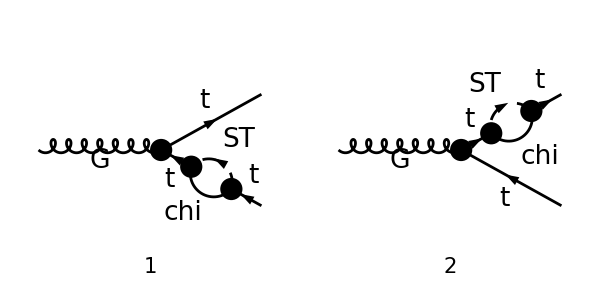

```mathematica
tops0 = CreateTopologies[0,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
tops = CreateTopologies[1,1->2,  ExcludeTopologies -> {TadpoleCTs,Tadpoles}];
processGGT =  {V[4]}->  {F[9],-F[9]};
allDiags = InsertFields[Join[tops0,tops],processGGT, InsertionLevel-> {Particles},ExcludeParticles->{V[1],V[4],S[1],S[2],S[3],V[2],V[3],F[7],F[6],F[5],F[8]}];
goodDiags=DiagramExtract[allDiags,{3,4}];
Paint[goodDiags,ColumnsXRows->{2,1},ImageSize->{ 600,300},PaintLevel->{Particles},Numbering->Simple,AutoEdit->True];
```

```mathematica
ampA=FCFAConvert[CreateFeynAmp[goodDiags,PreFactor->1,Truncated->True]/.{SUNT->FASUNT},IncomingMomenta->{p3},OutgoingMomenta->{p1,p2},LoopMomenta->{q},List->False,SUNIndexNames->{cc3,aa,bb},SUNFIndexNames->{a,c1,c2},DropSumOver->True,LorentzIndexNames->{ μ}, SMP->True,List->False,Contract->True,ChangeDimension->D,UndoChiralSplittings->True,FinalSubstitutions-> (M$FACouplings/.GS->gs)]/.{GS->gs,deltaCTL->0,deltaCTR->0};
ampB =FullSimplify[SUNSimplify[DiracSimplify[FCReplaceMomenta[ampA,{p3->-p1-p2}]]]]
```

in total: 2 Particles amplitudes

-gs yDM^2 T_c1c2^cc3 ((MT (γ·q).γ^μ.(γ̄)^7+(γ·q).(γ·p1).γ^μ.(γ̄)^6)/((p1^2-MT^2) (q^2-mChi^2).((p1+q)^2-mST^2))+(γ^μ.(γ·p2).(γ·q).(γ̄)^6-MT γ^μ.(γ·q).(γ̄)^6)/((p2^2-MT^2) (q^2-mChi^2).((p2+q)^2-mST^2)))

```mathematica
ampC =FCCanonicalizeDummyIndices[( TID[ampB,q,UsePaVeBasis->True,PaVeAutoReduce->False,ToPaVe->True]//Simplify),LorentzIndexNames-> {μ,ν}]
```

-ⅈ π^2 gs yDM^2 T_c1c2^cc3 (((MT (γ·p1).γ^μ.(γ̄)^7+(γ·p1).(γ·p1).γ^μ.(γ̄)^6) B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)-((MT γ^μ.(γ·p2).(γ̄)^6-γ^μ.(γ·p2).(γ·p2).(γ̄)^6) B_1(p2^2,mChi^2,mST^2))/(p2^2-MT^2))

```mathematica
Simplify[DiracSimplify[ampC,DiracOrder->False]]
```

-ⅈ π^2 gs yDM^2 T_c1c2^cc3 ((MT (γ·p1).γ^μ.(γ̄)^7 B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)+γ^μ.(γ̄)^6 ((p1^2 B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)+(p2^2 B_1(p2^2,mChi^2,mST^2))/(p2^2-MT^2))-(MT γ^μ.(γ·p2).(γ̄)^6 B_1(p2^2,mChi^2,mST^2))/(p2^2-MT^2))

```mathematica
Simplify[DiracSimplify[ampC,DiracOrder->True]]
```

ⅈ π^2 gs yDM^2 T_c1c2^cc3 (-((2 MT (γ̄)^7 p1^μ+p1^2 γ^μ.(γ̄)^6) B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)+(MT γ^μ.(γ·p1).(γ̄)^7 B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)+((MT γ^μ.(γ·p2).(γ̄)^6-p2^2 γ^μ.(γ̄)^6) B_1(p2^2,mChi^2,mST^2))/(p2^2-MT^2))

```mathematica
Collect[ampC,B1[a__],Simplify]
```

-ⅈ π^2 gs yDM^2 T_c1c2^cc3 (((MT (γ·p1).γ^μ.(γ̄)^7+(γ·p1).(γ·p1).γ^μ.(γ̄)^6) B_1(p1^2,mChi^2,mST^2))/(p1^2-MT^2)-((MT γ^μ.(γ·p2).(γ̄)^6-γ^μ.(γ·p2).(γ·p2).(γ̄)^6) B_1(p2^2,mChi^2,mST^2))/(p2^2-MT^2))